# Gravitational Memory Workbook

## Simon Thill, 2025

Code used while writing astrophysics senior thesis at Haverford College entitled “The Effect of Gravitational Memory on CMB Light.”

## Defining Variables and Functions

```mathematica
ClearAll["Global`*"]
```

### Rotation matrices and GW polarization tensors for a GW traveling along the z-axis.

```mathematica
Rz[ϕ_] := {{Cos[ϕ], -Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0},{0,0,1}} (*z-axis rotation*)
```

```mathematica
P = {{1,0,0},{0,-1,0}, {0,0,0}}; (*+ polarized wave*)
G = {{p,x,0},{x,-p,0}, {0,0,0}}; (*general wave polarization*)
X = {{0,1,0},{1,0,0}, {0,0,0}}; (*cross polarized wave*)
```

Applying the rotation matrix to + polarization. Tensors rotate as T’ = RTR^-1
To get the new tensor you apply the rotation matrix R and its inverse R^-1

```mathematica
Simplify[Rz[ϕ].P.Transpose[Rz[ϕ]]] //MatrixForm
```

(Cos[2 ϕ] | Sin[2 ϕ] | 0
Sin[2 ϕ] | -Cos[2 ϕ] | 0
0 | 0 | 0)

Rotations about the y and z-axes

```mathematica
Ry[α_] := {{Cos[α],0, Sin[α]}, {0,1,0},{-Sin[α], 0, Cos[α]}} (*y-axis rotation*)
Rx[α_] := {{1,0,0},{0, Cos[α], -Sin[α]}, {0,Sin[α],  Cos[α]}} (*x-axis rotation*)
```

```mathematica
MatrixForm[Rz[α]]
```

(Cos[α] | -Sin[α] | 0
Sin[α] | Cos[α] | 0
0 | 0 | 1)

### Variables and Functions

Constants: 
c=1, 
dG  Earth to GW source distance, 
tP time photon is received on Earth, 
tG time GW is received on Earth which we set to 0, 
(ϕ,θ) location on Earth’s sky where the photon is received
h0 GW strain amplitude measured on Earth
t time as measured on Earth 

Functions:
Functions are capitalized. A is the function that gives α for given parameters, RP is the function that gives rP.  
rP is the distance from GW source to photon
α is the angle between GW source and photon (measured up from GW propegation vector)
β is the azimuthal angle from the GW source to the photon 
dP is the distance from Earth to the photon
tmin is the initial time the photon encounters the GW
n is the vector pointing to point on the sky where the photon is found

```mathematica
c= 1.0;
tG = 0.0;
$Assumptions=dP>= 0.0&&dG>0.0&&h0>0.0&&tP>tG&&0.0<=θ<= π&&t∈Reals && 0.0<=ϕ<=2 π;
M[dP_, dG_] := If[dP>dG,ArcCos[dG/dP],0];
(*A[dP_, dG_, θ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] *)
DP[tP_, t_] := c(tP-t)
(*DP[tP_, t_] := If[tP>t,c(tP-t), 0]*) (*solves for if tP > t, but shouldn't be needed, although it did change the ϵ and h expresions a little*) 
Tmin[tG_, tP_, dG_,θ_] := (-c tG^2+2 dG tG +c tP^2 - 2 dG tP Cos[θ])/(-2 c tG + 2 dG + 2 c tP - 2 dG Cos[θ])
RP[dG_,tP_, t_,θ_] := Sqrt[dG^2+(tP-t)^2-2 dG(tP-t)Cos[θ] ]
n[θ_] := {Sin[θ], 0, Cos[θ]} (*2D looking vectore in x/z plane*)
v[θ_, ϕ_] := {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]} (*3D looking vector *)
```

```mathematica
$Assumptions
```

dP≥0.&&dG>0.&&h0>0.&&tP>0.&&0.≤θ≤π&&t∈ℝ&&0.≤ϕ≤2 π

Functions for α and β, which are related to polar angles in the GW source’s coordinate system. These are the angles we rotate through to relate the polarization metric seen at Earth to the polarization metric seen by a photon at a given time.

```mathematica
A[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ]Cos[ϕ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ]Cos[ϕ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ]Cos[ϕ])/(dG - dP Cos[θ])]-π]] 
B[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ]Sin[ϕ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ]Sin[ϕ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ]Sin[ϕ])/(dG - dP Cos[θ])]-π]]
```

The trig expressions  Sin[2 ArcTan[x]] , Cos[2 ArcTan[x]], and  Cos[4 ArcTan[x]] appears frequently in our code. Here, we define functions which can be used to simplify these expressions automatically.

```mathematica
SinSimp[opp_, adj_] := FullSimplify[2*opp/Sqrt[adj^2+opp^2]*adj/Sqrt[adj^2+opp^2]] (*Simplifies Sin[2ArcTan[opp/adj]]*)(*Sin(2x) = 2CosxSinx*)
CosSimp[opp_, adj_] := FullSimplify[(adj/Sqrt[adj^2+opp^2])^2-(opp/Sqrt[adj^2+opp^2])^2] (*Simplifies Cos[2ArcTan[opp/adj]]*)(*Cos(2x) = Cos^2(x) - Sin^2(x)*)
CosSimp4AT[opp_, adj_] := 8 (adj/Sqrt[adj^2+opp^2])^4-8 (adj/Sqrt[adj^2+opp^2])^2+1 (*Cos[4x] = 8 Cos[x]^2-8 Cos[x]^2+1)*)
```

#### Testing functions

```mathematica
Manipulate[Labeled[Plot[A[DP[tP, t] , dG, θ, ϕ],{θ,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", t = ",NumberForm[t,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,50},{tP,0.1,10},{t,-10,-0.1},{ϕ,0,2π}] (*Plot of the angle α. This contains If statments so it's important to make sure the final plot is continuous.*)
```

```mathematica
Manipulate[Labeled[PolarPlot[tP - Tmin[tG, tP, dG,θ] ,{θ,0, 2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,4}] (*This is a polar plot of the total amout of time a photon has spent in the perturbed metric as a function of the distance to the GW and the time the photon in recived on Earth. The time the GW passed is t=0 and the GW source is along the z-axis (θ=0).*)
```

## Isotropic, Plus Polarized Metric in 2D Simplification

### GW Metric

Simplifying to 2D. Here, ϕ = β = 0 and we only need to consider α. We also consider an isotropic GW.

```mathematica
P // MatrixForm (*plus-polarized GW polarization metric*)
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
Ε[α_] := Ry[-α].P.Transpose[Ry[-α]] (*Polarization of a + GW at an angle α.*)
Ε[α] //MatrixForm
```

(Cos[α]^2 | 0 | Cos[α] Sin[α]
0 | -1 | 0
Cos[α] Sin[α] | 0 | Sin[α]^2)

```mathematica
ϵ = FullSimplify[Ε[A[DP[tP,t], dG, θ,0]]]; (*plugging in α*)
MatrixForm[ϵ]
```

((dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | 1/2 Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]
0 | -1 | 0
1/2 Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]] | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
ϵ = ({{(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), 0, 1/2 SinSimp[(-t+tP) Sin[θ],dG+(t-tP) Cos[θ]]}, {0, -1, 0}, {1/2 SinSimp[(-t+tP) Sin[θ],dG+(t-tP) Cos[θ]], 0, ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}}); (*applying trig simplifications*)
MatrixForm[ϵ]
```

((dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
0 | -1 | 0
-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
h2DIso= FullSimplify[1/RP[dG,tP, t,θ] ϵ ];(*full expression for Subscript[h, ij], without multiplying by initial amplitude h0*dG*)
MatrixForm[h2DIso]
```

((dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
0 | -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0
-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)))

### Redshift

```mathematica
n[θ] (*2D looking vectore in x/z plane*)
```

{Sin[θ],0,Cos[θ]}

```mathematica
FullSimplify[n[θ].Transpose[n[θ].h2DIso]] (*applying n^i n^j*)
```

(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
HSimp[t_] := (dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)); (*n^i n^j Subscript[h, ij] as a function of time*)
```

```mathematica
ζSimp = FullSimplify[HSimp[Tmin[tG, tP, dG,θ]]] (*proportial to final redshfit*)
```

(8 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)

```mathematica
ndotR = FullSimplify[Cos[π - θ - A[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,0]]] (*dot product of n and R when the photon first encounters the GW*)
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
FullSimplify[-1/2 1/Abs[1+ndotR] ζSimp ] (*full redshift equation*)
```

-((4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3))

```mathematica
zSimp[θ_, dG_, tP_] := -((4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3))
```

```mathematica
(*Redshift function*)
```

```mathematica
Manipulate[Labeled[Plot[zSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,400}]  (*Plot of redshift*)
```

### Cross-Polarized GW Redshift

#### GW Metric

```mathematica
X // MatrixForm
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 0)

```mathematica
Εx[α_] := Ry[-α].X.Transpose[Ry[-α]] (*Polarization of a + GW at an angle α.*)
Εx[α] //MatrixForm
```

(0 | Cos[α] | 0
Cos[α] | 0 | Sin[α]
0 | Sin[α] | 0)

```mathematica
ϵx = FullSimplify[Εx[A[DP[tP,t], dG, θ,0]]]; (*plugging in α*)
MatrixForm[ϵx]
```

(0 | Piecewise[{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 0
Piecewise[{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])]-π]]]
0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])]-π]]] | 0)

```mathematica
hxSimp= FullSimplify[1/RP[dG,tP, t,θ] ϵx ];(*full expression for Subscript[h, ij], without multiplying by initial amplitude h0*dG*)
MatrixForm[hxSimp]
```

(0 | Piecewise[{{-Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}] | 0
Piecewise[{{-Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}] | 0 | Piecewise[{{((-t+tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), (dG+t≥tP&&θ>0)||(dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]≤2 π)}, {((t-tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), True}}]
0 | Piecewise[{{((-t+tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), (dG+t≥tP&&θ>0)||(dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]≤2 π)}, {((t-tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), True}}] | 0)

#### Redshift

```mathematica
n[θ] (*2D looking vectore in x/z plane*)
```

{Sin[θ],0,Cos[θ]}

```mathematica
FullSimplify[n[θ].Transpose[n[θ].hxSimp]] (*applying n^i n^j*)
```

0

There is no redshift due to a cross polarized wave in the x/z plane of our geometry. This is because when a  GW stretches and compresses spacetime there are four nodes which are not affected. For a cross-polarized wave (traveling along the z-axis), all points in the x/z plane are not affected. There will be a redshift effect in 3D

### Testing redshift results

Polarization component behavior.

```mathematica
FullSimplify[n[θ].Transpose[n[θ].ϵ]]
```

(dG^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])

```mathematica
ϵ2D[t_] := (dG^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
```

```mathematica
FullSimplify[ϵ2D[Tmin[tG, tP, dG,θ]]]
```

(4 dG^2 (dG+tP-dG Cos[θ])^2 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^2)

```mathematica
Manipulate[Labeled[Plot[(4 dG^2 (dG+tP-dG Cos[θ])^2 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^2),{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,400}]
```

```mathematica
Limit[(4 dG^2 (dG+tP-dG Cos[θ])^2 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^2),tP->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

One on R behavior

```mathematica
Manipulate[Labeled[Plot[1/RP[dG,tP, Tmin[tG, tP, dG,θ],θ] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,400}]
```

```mathematica
Limit[1/RP[dG,tP, Tmin[tG, tP, dG,θ],θ],tP->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

## Isotropic, Plus Polarized Metric in 2D binary’s plane: Work in Progress

ϕ = π/2
α = 0

```mathematica
A[DP[tP,t], dG, θ,ϕ]
```

If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ] Cos[ϕ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ] Cos[ϕ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ] Cos[ϕ])/(dG-(-t+tP) Cos[θ])]-π]]

```mathematica
Simplify[A[DP[tP,t], dG, θ,π/2]]
```

Piecewise[{{-π, dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]>2 π}, {π, (dG+t≥tP&&θ≤0)||(dG+t<tP&&θ≤ArcCos[dG/(-t+tP)])}, {0, True}}]

```mathematica
Manipulate[Labeled[Plot[A[DP[tP, t] , dG, θ, π/2],{θ,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", t = ",NumberForm[t,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,50},{tP,0.1,10},{t,-10,-0.1},{ϕ,0,2π}]
```

check this!! I think α should just be 0 for all times.

```mathematica
Clear[HyzIso]
```

```mathematica
hyzIso = Simplify[Rx[B[DP[tP,t], dG, θ,π/2]].Ry[-A[DP[tP,t], dG, θ,π/2]].(P/RP[dG,tP, t,θ]).Transpose[Ry[-A[DP[tP,t], dG, θ,π/2]]].Transpose[Rx[B[DP[tP,t], dG, θ,π/2]]]];
MatrixForm[hyzIso]
```

(1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0 | 0
0 | -(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | Piecewise[{{Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]>2 π}, {-Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), True}}]
0 | Piecewise[{{Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]>2 π}, {-Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), True}}] | -((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)))

```mathematica
Simplify[v[θ, π/2].Transpose[v[θ,π/2].hyzIso]]
```

-(Sin[θ] (dG^2 Sin[θ]-2 dG tP Cos[θ] Sin[θ]+2 t^2 Cos[θ]^2 Sin[θ]-4 t tP Cos[θ]^2 Sin[θ]+2 tP^2 Cos[θ]^2 Sin[θ]+dG t Sin[2 θ]-Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]))/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
Hyz[t_] := -(Sin[θ] (dG^2 Sin[θ]-2 dG tP Cos[θ] Sin[θ]+2 t^2 Cos[θ]^2 Sin[θ]-4 t tP Cos[θ]^2 Sin[θ]+2 tP^2 Cos[θ]^2 Sin[θ]+dG t Sin[2 θ]-Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]))/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
```

```mathematica
ζyz = FullSimplify[Hyz[Tmin[tG, tP, dG,θ]]]
```

-(8 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)

```mathematica
χ[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] (*angle between n and R*)
```

```mathematica
vdotRyz = FullSimplify[Cos[π - θ - χ[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,π/2]]]
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
FullSimplify[-1/2 1/Abs[1+vdotRyz] ζyz ] (*full redshift equation*)
```

(4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)

```mathematica
ZyzSimp[θ_, dG_, tP_] := (4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)
```

```mathematica
Manipulate[Labeled[Plot[ZyzSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,20},{tP,0.01,20}]  (*Plot of redshift*)
```

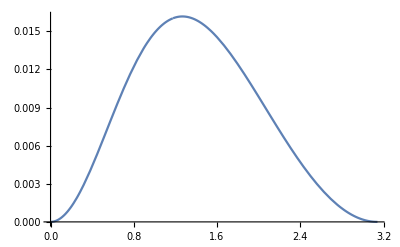

```mathematica
Plot[ZyzSimp[θ, 1, 4],{θ,0,π}]
```

## 3D, Isotropic, Plus-Polarised Wave: Work in Progress

```mathematica
h3DIso = Simplify[Rx[B[DP[tP,t], dG, θ,ϕ]].Ry[-A[DP[tP,t], dG, θ,ϕ]].(P/RP[dG,tP, t,θ]).Transpose[Ry[-A[DP[tP,t], dG, θ,ϕ]]].Transpose[Rx[B[DP[tP,t], dG, θ,ϕ]]]];
MatrixForm[h3DIso]
```

((dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) | Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]
Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))
Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) | -((t-tP)^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

### Applying Trig Simplifications

```mathematica
SinSimp[opp, adj]  (*Simplifies Sin[2ArcTan[opp/adj]]*)
```

(2 adj opp)/(adj^2+opp^2)

```mathematica
h3DIso = FullSimplify[({{(dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], Piecewise[{{-SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]}, {Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)SinSimp[(-t+tP) Sin[θ] Sin[ϕ], dG+(t-tP) Cos[θ]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))}, {Piecewise[{{-SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)SinSimp[(-t+tP) Sin[θ] Sin[ϕ], dG+(t-tP) Cos[θ]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), -((t-tP)^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}})];
```

```mathematica
MatrixForm[h3DIso]
```

((dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) | Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]
Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | ((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))
Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | ((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

### Considering If statements

In all cases, the different between the two possible IF statements is a negative sign.

(dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)

(dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP) 
θ is always greater than 0 and is ill-defined when it equals 0.

(θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP)
If dG+t<tP then dG+t≥tP must be false. tP-t = dP (distance from Earth to the photon), so this is saying dG < dP.

(θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)
The max value of θ is π and if dP > dG, ArcCos[dG/dP]<π, so θ+ArcCos[dG/(-t+tP)]< 2π.
What this If statement is saying is that if dP > dG (the distance from Earth to the photon is larger than the distance to the GW source), there is a cuttoff angle given by ArcCos[dG/dP] below which there is a sign flip for some entries of h_ij.

```mathematica
h3DIso = ({{(dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)), Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}], Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]}, {Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}], (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), ((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}, {Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], ((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ] ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}});
```

### Redshift

```mathematica
v[θ, ϕ] (*3D looking vector *)
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
Simplify[v[θ, ϕ].Transpose[v[θ,ϕ].h3DIso]] (*applying 3D looking vector twice*)
```

Cos[θ] Cos[ϕ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]+Cos[ϕ] (Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]^2 Sin[ϕ]+Cos[ϕ] Sin[θ] (Cos[θ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}])+((dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ] Sin[ϕ])+(2 (t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Sin[θ]^2 Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Cos[θ]^2 ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))

```mathematica
H3DIso[t_] := Cos[θ] Cos[ϕ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]+Cos[ϕ] (Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]^2 Sin[ϕ]+Cos[ϕ] Sin[θ] (Cos[θ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}])+((dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ] Sin[ϕ])+(2 (t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Sin[θ]^2 Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Cos[θ]^2 ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))
```

```mathematica
ζ3DIso = Simplify[H3DIso[Tmin[tG, tP, dG,θ]]]
```

1/2 Sin[θ] (2 Cos[θ] Cos[ϕ] (Piecewise[{{(2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+2 Cos[ϕ] (Cos[θ] (Piecewise[{{(2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+(2 (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ])+(8 tP (2 dG+tP) Cos[θ] (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Sin[θ] (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(4 (dG+tP-dG Cos[θ]) Sin[θ] Sin[ϕ]^2 (-(dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ] (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

```mathematica
χ[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] (*angle between n and R*)
```

```mathematica
vdotR3D = FullSimplify[Cos[π - θ - χ[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,ϕ]]]
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
Simplify[-1/2 1/Abs[1+vdotR3D] ζ3DIso ] (*full redshift equation*)
```

-((Sin[θ] (2 Cos[θ] Cos[ϕ] (Piecewise[{{(2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+2 Cos[ϕ] (Cos[θ] (Piecewise[{{(2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+(2 (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ])+(8 tP (2 dG+tP) Cos[θ] (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Sin[θ] (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(4 (dG+tP-dG Cos[θ]) Sin[θ] Sin[ϕ]^2 (-(dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ] (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))))/(4 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))

```mathematica
z3DIsoTrigandIfSimp[θ_,ϕ_, dG_, tP_] := -((Sin[θ] (2 Cos[θ] Cos[ϕ] (Piecewise[{{(2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+2 Cos[ϕ] (Cos[θ] (Piecewise[{{(2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((2 tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+(2 (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ])+(8 tP (2 dG+tP) Cos[θ] (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Sin[θ] (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(4 (dG+tP-dG Cos[θ]) Sin[θ] Sin[ϕ]^2 (-(dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]&&2 dG^2<tP^2+2 dG^2 Cos[θ]}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ]^2 Sin[2 ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ] (4 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[2 ϕ]-tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))))/(4 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))
```

```mathematica
z3DIso[θ_,ϕ_, dG_, tP_] := -((Sin[θ] (Cos[θ] Cos[ϕ] (Piecewise[{{(Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ]+Cos[ϕ] (Cos[θ] (Piecewise[{{(Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}])+(2 (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ])+(8 (dG+tP-dG Cos[θ])^3 Sin[θ] Sin[ϕ]^2 (-(dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(2 tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ] (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(2 Cos[θ] (dG+tP-dG Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Sin[θ] Sin[ϕ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/(2 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))
```

### Small Angle Approximation

Taking the limit for θ -> 0. This gives a small patch of sky around the GW source as viewed from Earth. ϕ can still vary from 0 to 2π.  Cos[θ] -> 1 and Sin[θ] -> θ

```mathematica
h3DIsoApprox = ({{(dG+(t-tP) 1)^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) ((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 (θ)^2)), Piecewise[{{((t-tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/(((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {-(((t-tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/(((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2)))), True}}], Piecewise[{{((t-tP) (dG+(t-tP) 1) Cos[ϕ] θ)/(((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {((-t+tP) (dG+(t-tP) 1) Cos[ϕ] θ)/(((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2))), True}}]}, {Piecewise[{{((t-tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/(((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {-(((t-tP)^2 Cos[ϕ] θ^2 Sin[ϕ])/(((dG+(t-tP)1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2)))), True}}], (-(dG+(t-tP) 1)^2+((t-tP)^4 Cos[ϕ]^2 θ^4 Sin[ϕ]^2)/((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) ((dG+(t-tP) 1)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), ((t-tP) (dG+(t-tP) 1) θ ((dG+(t-tP) 1)^2+2 (t-tP)^2 Cos[ϕ]^2 θ^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) ((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) ((dG+(t-tP) 1)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))}, {Piecewise[{{((t-tP) (dG+(t-tP) 1) Cos[ϕ] θ)/(((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP)1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2))), (θ≤ArcCos[dG/(-t+tP)])&&(dG+t<tP)}, {((-t+tP) (dG+(t-tP) 1) Cos[ϕ] θ)/(((dG+(t-tP)1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) √((dG^2+(t-tP)^2+2 dG (t-tP) 1) (1+((t-tP)^2 θ^2 Sin[ϕ]^2)/(dG+(t-tP) 1)^2))), True}}], ((t-tP) (dG+(t-tP) 1) θ ((dG+(t-tP) 1)^2+2 (t-tP)^2 Cos[ϕ]^2 θ^2) Sin[ϕ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) ((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) ((dG+(t-tP) 1)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), ((t-tP)^2 (dG+(t-tP) 1)^2 Cos[2 ϕ] θ^2-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) 1) ((dG+(t-tP) 1)^2+(t-tP)^2 Cos[ϕ]^2 θ^2) ((dG+(t-tP) 1)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))}});
```

```mathematica
vApprox[θ_, ϕ_] := {Cos[ϕ] θ,θ Sin[ϕ],1}
```

```mathematica
vApprox[θ, ϕ]
```

{θ Cos[ϕ],θ Sin[ϕ],1}

### Approximate Redshift (small θ approximation)

```mathematica
Simplify[vApprox[θ, ϕ].Transpose[vApprox[θ,ϕ].h3DIsoApprox]] (*applying approximate 3D looking vector twice*)
```

((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
H3DIsoApprox[t_] := ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))
```

```mathematica
Tmin[tG, tP, dG,θ]
```

(tP^2-2 dG tP Cos[θ])/(2 dG+2 tP-2 dG Cos[θ])

```mathematica
ζ3DIso = Simplify[H3DIsoApprox[(tP^2-2 dG tP 1)/(2 dG+2 tP-2 dG 1)]] (*plugging in approximate Tmin for small θ*)
```

(θ (4 tP^6 (2 dG+tP)^2 θ Cos[2 ϕ]+4 tP^3 (2 dG+tP) θ (tP^4+2 tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+2 tP Cos[ϕ] (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (tP^4+tP^2 (2 dG+tP)^2 θ^2 Sin[ϕ]^2)+2 tP Cos[ϕ] (2 tP^3 θ Cos[ϕ]+(tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) (tP^4+tP^2 (2 dG+tP)^2 θ^2 Sin[ϕ]^2)-2 tP^3 θ Sin[ϕ] (2 tP (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-2 (2 dG+tP) (tP^4+2 tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-2 tP (2 dG+tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3-tP^2 Cos[ϕ] (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))-tP^4 (2 dG+tP)^4 θ^3 Sin[2 ϕ]^2))/(2 tP^5 (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
χApprox[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP θ)/(dG - dP 1)]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP θ)/(dG - dP 1)],ArcTan[(dP θ)/(dG - dP 1)]-π]] (*approx angle between n and R*)
```

```mathematica
vdotR3DApprox = FullSimplify[Cos[π - θ - χApprox[DP[tP,(tP^2-2 dG tP 1)/(2 dG+2 tP-2 dG 1)], dG, θ,ϕ]]] (*also manually plugging in approximate Tmin*)
```

Piecewise[{{-Cos[θ-ArcTan[θ+(2 dG θ)/tP]], θ+ArcCos[(2 dG)/(2 dG+tP)]≤2 π&&θ>ArcCos[(2 dG)/(2 dG+tP)]}, {Cos[θ-ArcTan[θ+(2 dG θ)/tP]], True}}]

```mathematica
FullSimplify[-1/2 1/Abs[1+vdotR3DApprox] ζ3DIso ] (*full redshift equation*)
```

```mathematica
z3DIsoApprox[θ_,ϕ_, dG_, tP_] := -((θ (4 tP^6 (2 dG+tP)^2 θ Cos[2 ϕ]+4 tP^3 (2 dG+tP) θ (tP^4+2 tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+2 tP Cos[ϕ] (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (tP^4+tP^2 (2 dG+tP)^2 θ^2 Sin[ϕ]^2)+2 tP Cos[ϕ] (2 tP^3 θ Cos[ϕ]+(tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-(2 tP (2 dG+tP) θ Cos[ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) (tP^4+tP^2 (2 dG+tP)^2 θ^2 Sin[ϕ]^2)-2 tP^3 θ Sin[ϕ] (2 tP (tP^4+tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-2 (2 dG+tP) (tP^4+2 tP^2 (2 dG+tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-2 tP (2 dG+tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3-tP^2 Cos[ϕ] (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[(2 dG)/(2 dG+tP)]}, {-((2 dG+tP)^2 θ^2 Sin[2 ϕ])/((tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) √(tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2))-tP^4 (2 dG+tP)^4 θ^3 Sin[2 ϕ]^2))/(4 tP^5 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[θ+(2 dG θ)/tP]], θ+ArcCos[(2 dG)/(2 dG+tP)]≤2 π&&θ>ArcCos[(2 dG)/(2 dG+tP)]}, {Cos[θ-ArcTan[θ+(2 dG θ)/tP]], True}}])] (tP^2+(2 dG+tP)^2 θ^2 Cos[ϕ]^2) (tP^2+(2 dG+tP)^2 θ^2 Sin[ϕ]^2)))
```

### Plotting

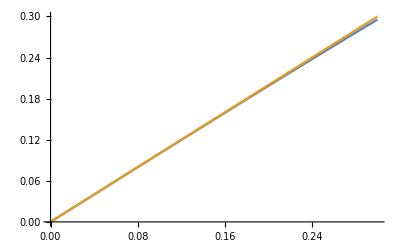

```mathematica
Plot[{Sin[x],x},{x,0,0.3}]
```

```mathematica
Manipulate[Labeled[Plot[z3DIsoApprox[θ, ϕ, dG, tP] ,{θ,0, 0.3}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}, {ϕ,0,2π}]
```

Discontinuity when dG/tP > 10 for a max θ of 0.3. It might be physical, from the instant heavystep function? 
Example: dG = 19.6, tP = 0.45, ϕ = 0, cutoff at θ=0.15

```mathematica
24.4/2.3
```

10.6087

```mathematica
N[π/2]
```

1.5708

```mathematica
Manipulate[Labeled[Plot[z3DIsoTrigandIfSimp[θ, ϕ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}, {ϕ,0,2π}]
```

Discontinuity at dG = 0.1, tP=28, ϕ=0, goes to 0 at θ = π/2
Discontinuity when tP >> dG for θ = π/2, but only when ϕ is not π/2 
Same discontinuity for any value of tP and dG. Example: dG = 4.65, tP = 11.3, ϕ = 1.55, θ = 1.0

```mathematica
Manipulate[Labeled[Plot[z3DIso[θ, ϕ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}, {ϕ,0,2π}]
```

```mathematica
Manipulate[Labeled[Plot[zSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}]
```

```mathematica
Manipulate[Labeled[SphericalPlot3D[z3DIso[θ, ϕ, dG, tP] ,{θ,0.001, π-0.001},{ϕ,0.001,2π-0.001}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],}],Top],{dG,0.1,30},{tP,0.01,40}]
```

Max::nord: Invalid comparison with 6.05793-0.611681 ⅈ attempted.

Max::nord: Invalid comparison with 0.225257-0.611681 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Min::nord2: Comparison of Max[-6.05793+0.611681 ⅈ,-0.225257+0.611681 ⅈ,0.125263] and ∞ is invalid.

Min::nord2: Comparison of Max[-6.05793+0.611681 ⅈ,-0.225257+0.611681 ⅈ,0.000405264] and ∞ is invalid.

Min::nord2: Comparison of Max[0.0207383,6.05793-0.611681 ⅈ] and ∞ is invalid.

General::stop: Further output of Min::nord2 will be suppressed during this calculation.

Max::nord: Invalid comparison with 6.05793-3.74048 ⅈ attempted.

Max::nord: Invalid comparison with 0.225257-3.74048 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Min::nord2: Comparison of Max[-6.05793+3.74048 ⅈ,-0.225257+3.74048 ⅈ,3.1933] and ∞ is invalid.

Min::nord2: Comparison of Max[3.1933,6.05793-3.74048 ⅈ] and ∞ is invalid.

Min::nord2: Comparison of Max[0.225257-3.74048 ⅈ,3.1933] and ∞ is invalid.

General::stop: Further output of Min::nord2 will be suppressed during this calculation.

```mathematica
Manipulate[Labeled[SphericalPlot3D[1,{θ,0,Pi},{φ,0,2 Pi},ColorFunction->Function[{θ,ϕ},z3DIso[θ, ϕ, dG, tP]],ColorFunctionScaling->True,PlotPoints->50,Lighting->"Neutral",Mesh->None],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],}],Top],{dG,0.1,30},{tP,0.01,40}]
```

### Deflection angle (small θ approximation)

```mathematica
H3DIsoApprox[t_, tP_, θ_, ϕ_] := ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))
```

```mathematica
H3DIsoApproxV2[t_,tP_,θ_,ϕ_,dG_]:=Module[
{
A=t-tP,
B=dG+t-tP,
cosϕ=Cos[ϕ],
sinϕ=Sin[ϕ],
θ2=θ^2,
cosϕ2=Cos[ϕ]^2,
sinϕ2=Sin[ϕ]^2,
absB,
sqrtTerm,
piecewiseCond1,
piecewiseCond2,
piecewiseVal
},

absB=Abs[B];
sqrtTerm=Sqrt[B^2+A^2 θ2 sinϕ2];
piecewiseCond1=θ<=ArcCos[dG/(-t+tP)]&&B+t<tP;

piecewiseVal=Piecewise[{
{(A B θ cosϕ (B^2+A^2 θ2 cosϕ2))/sqrtTerm,piecewiseCond1},
{-(A B θ cosϕ (B^2+A^2 θ2 cosϕ2))/sqrtTerm,True}
}];

(*Now write the full formula as a sum of terms using these variables*)(A^2 B^2 θ2 Cos[2 ϕ]+A B θ2 (B^2+2 A^2 θ2 cosϕ2) sinϕ2+θ absB cosϕ (B^2+A^2 θ2 cosϕ2) piecewiseVal+θ absB cosϕ (θ absB cosϕ+(B^2+A^2 θ2 cosϕ2) piecewiseVal) (B^2+A^2 θ2 sinϕ2)+θ ((B^2+A^2 θ2 cosϕ2) piecewiseVal)-(1/4) A^4 θ^4 Sin[2 ϕ]^2)/(absB (B^2+A^2 θ2 cosϕ2) (B^2+A^2 θ2 sinϕ2))]
```

```mathematica
Simplify[D[H3DIsoApproxV2[t, tP, θ, ϕ, dG],tP]]
```

(-Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)-Abs[dG+t-tP] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2) Abs'[dG+t-tP]+θ Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 (t-tP)^2 (dG+t-tP) θ Cos[2 ϕ]-2 (t-tP) (dG+t-tP)^2 θ Cos[2 ϕ]+(-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{1/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))θ Cos[ϕ] (-((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))+2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {1/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))θ Cos[ϕ] ((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)-2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{1/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))θ Cos[ϕ] (-((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))+2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {1/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))θ Cos[ϕ] ((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)-2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+(t-tP) (dG+t-tP) θ (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(t-tP) θ ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(dG+t-tP) θ ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+(t-tP)^3 θ^3 Sin[2 ϕ]^2-Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Abs'[dG+t-tP]-Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{1/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))θ Cos[ϕ] (-((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))+2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {1/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))θ Cos[ϕ] ((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)-2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])-θ Cos[ϕ] Abs'[dG+t-tP])))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
Simplify[D[H3DIsoApproxV2[t, tP, θ, ϕ, dG],θ]]
```

(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 (t-tP)^2 (dG+t-tP)^2 θ Cos[2 ϕ]+2 (t-tP)^2 θ^2 Cos[ϕ]^2 (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+2 (t-tP)^2 θ^2 Abs[dG+t-tP] Cos[ϕ]^3 (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) Cos[ϕ] ((dG+t-tP)^4+3 (t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2+2 (t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {((t-tP) (dG+t-tP) Cos[ϕ] (-(dG+t-tP)^4-3 (t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2-2 (t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}])+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) Cos[ϕ] ((dG+t-tP)^4+3 (t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2+2 (t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {((t-tP) (dG+t-tP) Cos[ϕ] (-(dG+t-tP)^4-3 (t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2-2 (t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}])+2 (t-tP) (dG+t-tP) θ ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+2 (t-tP)^2 θ^2 Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])) Sin[ϕ]^2+Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (Abs[dG+t-tP] Cos[ϕ]+2 (t-tP)^2 θ Cos[ϕ]^2 (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) Cos[ϕ] ((dG+t-tP)^4+3 (t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2+2 (t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {((t-tP) (dG+t-tP) Cos[ϕ] (-(dG+t-tP)^4-3 (t-tP)^2 (dG+t-tP)^2 θ^2 Cos[ϕ]^2-2 (t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}])) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-(t-tP)^4 θ^3 Sin[2 ϕ]^2+(t-tP)^3 (dG+t-tP) θ^3 Sin[2 ϕ]^2)-2 (t-tP)^2 θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2 ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)-2 (t-tP)^2 θ Cos[ϕ]^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
Simplify[H3DIsoApproxV2[t, tP, θ, ϕ, dG]-H3DIsoApprox[t, tP, θ, ϕ]] (*run this!*)
```

θ (-2 Cos[ϕ] (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+Cos[ϕ] (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(Cos[ϕ] (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]))/((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+((dG+t-tP)^2 θ Sin[ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP) (dG+t-tP) θ ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP)^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-θ (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[2 ϕ])

```mathematica
Simplify[θ (-2 Cos[ϕ] (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+Cos[ϕ] (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(Cos[ϕ] (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]))/((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+((dG+t-tP)^2 θ Sin[ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP) (dG+t-tP) θ ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP)^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-θ (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[2 ϕ])]
```

θ (-2 Cos[ϕ] (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+Cos[ϕ] (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(Cos[ϕ] (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+2 t<2 tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2))/(√((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]))/((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+((dG+t-tP)^2 θ Sin[ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP) (dG+t-tP) θ ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP)^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-θ (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[2 ϕ])

```mathematica
FullSimplify[θ (-2 Cos[ϕ] A+Cos[ϕ] A+A/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(Cos[ϕ] A)/((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+((dG+t-tP)^2 θ Sin[ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP) (dG+t-tP) θ ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP)^4 θ^5 Cos[ϕ]^2 Sin[ϕ]^4)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-θ (A) Sin[2 ϕ])]
```

$Aborted

#### x-deflection

∂/(∂ x) = Sin[θ]Cos[ϕ]∂/(∂ r) + 1/r Cos[ϕ]Cos[θ]∂/(∂ θ)- 1/r Sin[ϕ]/Sin[θ]∂/(∂ ϕ)

either write r in terms of tP and t? or write x in terms of θ, ϕ, etc? Try both and compare. 
In this case, r = DP[tP,  t] = c(tP-t). You can take the derivative with respect to tP or t, they are equal and opposite

```mathematica
Simplify[D[H3DIsoApprox[t, tP, θ, ϕ],tP]+D[H3DIsoApprox[t, tP, θ, ϕ],t]]
```

0

θ Cos[ϕ] D[H3DIsoApprox[t, tP, θ, ϕ],r] + 1/r Cos[ϕ] D[H3DIsoApprox[t, tP, θ, ϕ],θ] - 1/r Sin[ϕ]/θ D[H3DIsoApprox[t, tP, θ, ϕ],ϕ]

```mathematica
θ Cos[ϕ] D[H3DIsoApprox[t, tP, θ, ϕ],tP] + 1/(tP-t)Cos[ϕ] D[H3DIsoApprox[t, tP, θ, ϕ],θ] - 1/(tP-t)Sin[ϕ]/θ D[H3DIsoApprox[t, tP, θ, ϕ],ϕ]
```

```mathematica
(*Define θ and ϕ as functions of x and y, in the flat-sky approximation?? *)
θ[x_,y_]:= Sqrt[x^2+y^2]
```

```mathematica
ϕ[x_,y_]:=ArcTan[y/x]
```

Use Set inseat of SetDelayed. 
Use floating point numbers 
Compile? - maybe no. many Mathematica functions like Table, Plot, NIntegrate, and so on automatically compile their arguments, so you won’t see any improvement when passing them compiled versions of your code.
Module? - or use Block in stead (should be the same but faster) 
Simplfy, use a TimeConstraint
Collect[expression,{a,b,Erfc[_]},Simplify]. This way you prevent mathematica from working on parts of the problem you know won’t simplify like a, b, Erfc.
FullSimplify[Simplify[expr]]
Simplify[Simplify[expr, ComplexityFunction→LeafCount?, TimeConstraint -> 0.1]] run time constraint with Off[General::stop];
Notes on integrating - https://support.wolfram.com/12485 

Piecewise instead of multiple Ifs

```mathematica
Piecewise
```

```mathematica
hijdr = D[H3DIsoApprox[t, tP, θ, ϕ],tP]
```

-(((-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2))-((-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2) Abs'[dG+t-tP])/(Abs[dG+t-tP]^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(-2 (t-tP)^2 (dG+t-tP) θ^2 Cos[2 ϕ]-2 (t-tP) (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(t-tP)^3 θ^4 Sin[2 ϕ]^2-θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]-θ Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]-θ Cos[ϕ] Abs'[dG+t-tP])+θ^2 Sin[ϕ] ((t-tP) (dG+t-tP) (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]-(dG+t-tP)^2 (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-(t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-(dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-4 (t-tP)^3 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
Simplify[hijdr, TimeConstraint->1]
```

(-Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)-Abs[dG+t-tP] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2) Abs'[dG+t-tP]+θ Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 (t-tP)^2 (dG+t-tP) θ Cos[2 ϕ]-2 (t-tP) (dG+t-tP)^2 θ Cos[2 ϕ]+(t-tP) (dG+t-tP) θ (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(t-tP) θ ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(dG+t-tP) θ ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(θ Cos[ϕ] (-((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))-2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {(θ Cos[ϕ] ((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(t-tP)^3 θ^3 Sin[2 ϕ]^2-Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]-Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{(θ Cos[ϕ] (-((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))-2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {(θ Cos[ϕ] ((t-tP) (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+2 (t-tP) (dG+t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}])+θ (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) θ^2 Cos[ϕ] Sin[ϕ] (-2 dG^4-5 dG^3 t-3 dG^2 t^2+dG t^3+t^4+5 dG^3 tP+6 dG^2 t tP-3 dG t^2 tP-4 t^3 tP-3 dG^2 tP^2+3 dG t tP^2+6 t^2 tP^2-dG tP^3-4 t tP^3+tP^4+(-dG^2+(t-tP)^2) (t-tP)^2 θ^2 Sin[ϕ]^2+Cos[ϕ]^2 ((t-tP)^3 (dG+t-tP) θ^2+(t^4+6 t^2 tP^2+tP^4) θ^4 Sin[ϕ]^2)-t^3 tP θ^4 Sin[2 ϕ]^2-t tP^3 θ^4 Sin[2 ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((t-tP) θ^2 Cos[ϕ] Sin[ϕ] ((t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+2 (t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+4 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}]) Sin[ϕ]-θ Cos[ϕ] Abs'[dG+t-tP])+θ Sin[ϕ] ((t-tP) (dG+t-tP) (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]+2 (dG+t-tP)^2 (dG+t-tP+(t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-(t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-(dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-4 (t-tP)^3 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) θ^2 Cos[ϕ] Sin[ϕ] (-2 dG^4-5 dG^3 t-3 dG^2 t^2+dG t^3+t^4+5 dG^3 tP+6 dG^2 t tP-3 dG t^2 tP-4 t^3 tP-3 dG^2 tP^2+3 dG t tP^2+6 t^2 tP^2-dG tP^3-4 t tP^3+tP^4+(-dG^2+(t-tP)^2) (t-tP)^2 θ^2 Sin[ϕ]^2+Cos[ϕ]^2 ((t-tP)^3 (dG+t-tP) θ^2+(t^4+6 t^2 tP^2+tP^4) θ^4 Sin[ϕ]^2)-t^3 tP θ^4 Sin[2 ϕ]^2-t tP^3 θ^4 Sin[2 ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((t-tP) θ^2 Cos[ϕ] Sin[ϕ] ((t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+2 (t-tP) (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+4 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP])))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
Collec
```

## Testing

```mathematica
H3DIsoApprox[t_, tP_, θ_, ϕ_] := ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2)/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))
```

```mathematica
hijdr = D[H3DIsoApprox[t, tP, θ, ϕ],tP]
```

-(((-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2))-((-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) ((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(((t-tP)^2 (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ^2 Sin[ϕ] (-(dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP) (dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]+(t-tP)^4 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 (t-tP)^4 θ^4 Sin[2 ϕ]^2) Abs'[dG+t-tP])/(Abs[dG+t-tP]^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(-2 (t-tP)^2 (dG+t-tP) θ^2 Cos[2 ϕ]-2 (t-tP) (dG+t-tP)^2 θ^2 Cos[2 ϕ]+(t-tP) (dG+t-tP) θ^2 (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2-(dG+t-tP) θ^2 ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]^2+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(t-tP)^3 θ^4 Sin[2 ϕ]^2-θ Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]-θ Cos[ϕ] (θ Abs[dG+t-tP] Cos[ϕ]+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]+θ Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) ((-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP) (dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP) (dG+t-tP) θ Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2))/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+((dG+t-tP) θ Cos[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}])+θ (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]+θ ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) Sin[ϕ]-θ Cos[ϕ] Abs'[dG+t-tP])+θ^2 Sin[ϕ] ((t-tP) (dG+t-tP) (-2 (dG+t-tP)-4 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]-(dG+t-tP)^2 (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ]+2 (dG+t-tP) ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-(t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-(dG+t-tP) ((dG+t-tP)^2+2 (t-tP)^2 θ^2 Cos[ϕ]^2) Sin[ϕ]-4 (t-tP)^3 θ^4 Cos[ϕ]^2 Sin[ϕ]^3+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+Abs[dG+t-tP] Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))-((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ-ArcCos[dG/(-t+tP)]≤0&&dG+t-tP<0}, {((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Sin[ϕ]^2))/(2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(3/2))+((t-tP)^2 θ^2 Cos[ϕ] (-2 (dG+t-tP)-2 (t-tP) θ^2 Cos[ϕ]^2) Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(2 (t-tP) θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-Cos[ϕ] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) (Piecewise[{{((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 θ^2 Cos[ϕ] Sin[ϕ])/(((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)), True}}]) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) Abs'[dG+t-tP]))/(Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))

```mathematica
Off[General::stop];
```

```mathematica
Assuming[θ>ArcCos[dG/(-t+tP)], Simplify[Simplify[hijdr, TimeConstraint->1,ComplexityFunction->LeafCount], TimeConstraint->10, ComplexityFunction->LeafCount] ]
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP])))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdθ = D[H3DIsoApprox[t, tP, θ, ϕ],θ] ;
```

```mathematica
hijdθAsm = Assuming[θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP, Simplify[Simplify[hijdθ, TimeConstraint->1,ComplexityFunction->LeafCount], TimeConstraint->10, ComplexityFunction->LeafCount] ] (*partial derivative with respect to θ, with assumption*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+3 θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-32 dG t^2 θ^2-24 t^3 θ^2+64 dG t tP θ^2+72 t^2 tP θ^2-32 dG tP^2 θ^2-72 t tP^2 θ^2+24 tP^3 θ^2-6 t^3 θ^4+18 t^2 tP θ^4-18 t tP^2 θ^4+6 tP^3 θ^4+2 (t-tP)^2 θ^2 (16 dG+3 (t-tP) (4+θ^2)) Cos[4 ϕ]-3 (t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))

```mathematica
hijdθTr = Assuming[θ>ArcCos[dG/(-t+tP)], Simplify[Simplify[hijdθ, TimeConstraint->1,ComplexityFunction->LeafCount], TimeConstraint->10, ComplexityFunction->LeafCount] ] (*partial derivative with respect to θ, without assumption*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-32 Abs[dG+t-tP]^2 Cos[ϕ]^2 (dG^2+2 dG (t-tP)+(t-tP)^2 (1+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+8 dG^2 t^2 θ^2-16 dG t^3 θ^2-16 t^4 θ^2-16 dG^2 t tP θ^2+48 dG t^2 tP θ^2+64 t^3 tP θ^2+8 dG^2 tP^2 θ^2-48 dG t tP^2 θ^2-96 t^2 tP^2 θ^2+16 dG tP^3 θ^2+64 t tP^3 θ^2-16 tP^4 θ^2-6 t^4 θ^4+24 t^3 tP θ^4-36 t^2 tP^2 θ^4+24 t tP^3 θ^4-6 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+3 θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-4 dG^2+8 dG (t-tP)+(t-tP)^2 (8+3 θ^2)) Cos[4 ϕ]-3 t^4 θ^4 Cos[6 ϕ]+12 t^3 tP θ^4 Cos[6 ϕ]-18 t^2 tP^2 θ^4 Cos[6 ϕ]+12 t tP^3 θ^4 Cos[6 ϕ]-3 tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)+8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+4 dG^2 t^2 θ^2-8 dG t^3 θ^2-8 t^4 θ^2-8 dG^2 t tP θ^2+24 dG t^2 tP θ^2+32 t^3 tP θ^2+4 dG^2 tP^2 θ^2-24 dG t tP^2 θ^2-48 t^2 tP^2 θ^2+8 dG tP^3 θ^2+32 t tP^3 θ^2-8 tP^4 θ^2-2 t^4 θ^4+8 t^3 tP θ^4-12 t^2 tP^2 θ^4+8 t tP^3 θ^4-2 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]-t^4 θ^4 Cos[6 ϕ]+4 t^3 tP θ^4 Cos[6 ϕ]-6 t^2 tP^2 θ^4 Cos[6 ϕ]+4 t tP^3 θ^4 Cos[6 ϕ]-tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^3 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))

```mathematica
hijdϕ = D[H3DIsoApprox[t, tP, θ, ϕ],ϕ] ;
```

```mathematica
hijdϕAsm = Assuming[θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP, Simplify[Simplify[hijdϕ, TimeConstraint->1,ComplexityFunction->LeafCount], TimeConstraint->10, ComplexityFunction->LeafCount] ] (*partial derivative with respect to ϕ, with assumption*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

(θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-8 (dG+t-tP)^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] ((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-8 (t-tP)^2 θ^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))

```mathematica
hijdϕTr = Assuming[θ>ArcCos[dG/(-t+tP)], Simplify[Simplify[hijdϕ, TimeConstraint->1,ComplexityFunction->LeafCount], TimeConstraint->10, ComplexityFunction->LeafCount] ] (*partial derivative with respect to ϕ, without assumption*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

(θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-32 (dG+t-tP)^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ])-(16 √2 (t-tP)^4 θ^4 Abs[dG+t-tP]^2 Cos[ϕ]^2 Cos[2 ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2))/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-4 (dG+t-tP)^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ])-32 (t-tP)^2 θ^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2+8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-4 (t-tP)^2 θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] (-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))

```mathematica
hijdr = D[H3DIsoApprox[t, tP, θ, ϕ],tP] ;
```

```mathematica
hijdrAsm = Assuming[θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP, Simplify[Simplify[hijdr, TimeConstraint->1,ComplexityFunction->LeafCount], TimeConstraint->10, ComplexityFunction->LeafCount] ] (*partial derivative with respect to r, with assumption*)
```

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 10. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]+2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP])))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdrTr = ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP])))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)
```

((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP])))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdxAsm = θ Cos[ϕ] hijdrAsm + 1/(tP-t)Cos[ϕ] hijdθAsm  - 1/(tP-t)Sin[ϕ]/θ hijdϕAsm (*partial derivative of x, with assumption*)
```

(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+3 θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-32 dG t^2 θ^2-24 t^3 θ^2+64 dG t tP θ^2+72 t^2 tP θ^2-32 dG tP^2 θ^2-72 t tP^2 θ^2+24 tP^3 θ^2-6 t^3 θ^4+18 t^2 tP θ^4-18 t tP^2 θ^4+6 tP^3 θ^4+2 (t-tP)^2 θ^2 (16 dG+3 (t-tP) (4+θ^2)) Cos[4 ϕ]-3 (t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-8 (dG+t-tP)^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] ((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-8 (t-tP)^2 θ^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]+2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdxAsm = Simplify[Simplify[hijdxAsm, TimeConstraint->2,ComplexityFunction->LeafCount], TimeConstraint->20, ComplexityFunction->LeafCount]
```

Simplify::time: Time spent on a transformation exceeded 2. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 20. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+3 θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-32 dG t^2 θ^2-24 t^3 θ^2+64 dG t tP θ^2+72 t^2 tP θ^2-32 dG tP^2 θ^2-72 t tP^2 θ^2+24 tP^3 θ^2-6 t^3 θ^4+18 t^2 tP θ^4-18 t tP^2 θ^4+6 tP^3 θ^4+2 (t-tP)^2 θ^2 (16 dG+3 (t-tP) (4+θ^2)) Cos[4 ϕ]-3 (t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-8 (dG+t-tP)^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] ((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-8 (t-tP)^2 θ^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]+2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdxTr = θ Cos[ϕ] hijdrTr + 1/(tP-t)Cos[ϕ] hijdθTr  - 1/(tP-t)Sin[ϕ]/θ hijdϕTr (*partial derivative of x, withour assumption*)
```

(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-32 Abs[dG+t-tP]^2 Cos[ϕ]^2 (dG^2+2 dG (t-tP)+(t-tP)^2 (1+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+8 dG^2 t^2 θ^2-16 dG t^3 θ^2-16 t^4 θ^2-16 dG^2 t tP θ^2+48 dG t^2 tP θ^2+64 t^3 tP θ^2+8 dG^2 tP^2 θ^2-48 dG t tP^2 θ^2-96 t^2 tP^2 θ^2+16 dG tP^3 θ^2+64 t tP^3 θ^2-16 tP^4 θ^2-6 t^4 θ^4+24 t^3 tP θ^4-36 t^2 tP^2 θ^4+24 t tP^3 θ^4-6 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+3 θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-4 dG^2+8 dG (t-tP)+(t-tP)^2 (8+3 θ^2)) Cos[4 ϕ]-3 t^4 θ^4 Cos[6 ϕ]+12 t^3 tP θ^4 Cos[6 ϕ]-18 t^2 tP^2 θ^4 Cos[6 ϕ]+12 t tP^3 θ^4 Cos[6 ϕ]-3 tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)+8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+4 dG^2 t^2 θ^2-8 dG t^3 θ^2-8 t^4 θ^2-8 dG^2 t tP θ^2+24 dG t^2 tP θ^2+32 t^3 tP θ^2+4 dG^2 tP^2 θ^2-24 dG t tP^2 θ^2-48 t^2 tP^2 θ^2+8 dG tP^3 θ^2+32 t tP^3 θ^2-8 tP^4 θ^2-2 t^4 θ^4+8 t^3 tP θ^4-12 t^2 tP^2 θ^4+8 t tP^3 θ^4-2 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]-t^4 θ^4 Cos[6 ϕ]+4 t^3 tP θ^4 Cos[6 ϕ]-6 t^2 tP^2 θ^4 Cos[6 ϕ]+4 t tP^3 θ^4 Cos[6 ϕ]-tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^3 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-32 (dG+t-tP)^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ])-(16 √2 (t-tP)^4 θ^4 Abs[dG+t-tP]^2 Cos[ϕ]^2 Cos[2 ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2))/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-4 (dG+t-tP)^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ])-32 (t-tP)^2 θ^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2+8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-4 (t-tP)^2 θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] (-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdxTr = Simplify[Simplify[hijdxTr, TimeConstraint->2,ComplexityFunction->LeafCount], TimeConstraint->20, ComplexityFunction->LeafCount]
```

Simplify::time: Time spent on a transformation exceeded 2. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 20. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-32 Abs[dG+t-tP]^2 Cos[ϕ]^2 (dG^2+2 dG (t-tP)+(t-tP)^2 (1+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+8 dG^2 t^2 θ^2-16 dG t^3 θ^2-16 t^4 θ^2-16 dG^2 t tP θ^2+48 dG t^2 tP θ^2+64 t^3 tP θ^2+8 dG^2 tP^2 θ^2-48 dG t tP^2 θ^2-96 t^2 tP^2 θ^2+16 dG tP^3 θ^2+64 t tP^3 θ^2-16 tP^4 θ^2-6 t^4 θ^4+24 t^3 tP θ^4-36 t^2 tP^2 θ^4+24 t tP^3 θ^4-6 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+3 θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-4 dG^2+8 dG (t-tP)+(t-tP)^2 (8+3 θ^2)) Cos[4 ϕ]-3 t^4 θ^4 Cos[6 ϕ]+12 t^3 tP θ^4 Cos[6 ϕ]-18 t^2 tP^2 θ^4 Cos[6 ϕ]+12 t tP^3 θ^4 Cos[6 ϕ]-3 tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)+8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+4 dG^2 t^2 θ^2-8 dG t^3 θ^2-8 t^4 θ^2-8 dG^2 t tP θ^2+24 dG t^2 tP θ^2+32 t^3 tP θ^2+4 dG^2 tP^2 θ^2-24 dG t tP^2 θ^2-48 t^2 tP^2 θ^2+8 dG tP^3 θ^2+32 t tP^3 θ^2-8 tP^4 θ^2-2 t^4 θ^4+8 t^3 tP θ^4-12 t^2 tP^2 θ^4+8 t tP^3 θ^4-2 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]-t^4 θ^4 Cos[6 ϕ]+4 t^3 tP θ^4 Cos[6 ϕ]-6 t^2 tP^2 θ^4 Cos[6 ϕ]+4 t tP^3 θ^4 Cos[6 ϕ]-tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^3 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-32 (dG+t-tP)^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ])-(16 √2 (t-tP)^4 θ^4 Abs[dG+t-tP]^2 Cos[ϕ]^2 Cos[2 ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2))/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-4 (dG+t-tP)^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ])-32 (t-tP)^2 θ^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2+8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-4 (t-tP)^2 θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] (-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2)

```mathematica
hijdx = Piecewise[{{hijdxAsm,θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}},hijdxTr]
```

Piecewise[{{(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+3 θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-32 dG t^2 θ^2-24 t^3 θ^2+64 dG t tP θ^2+72 t^2 tP θ^2-32 dG tP^2 θ^2-72 t tP^2 θ^2+24 tP^3 θ^2-6 t^3 θ^4+18 t^2 tP θ^4-18 t tP^2 θ^4+6 tP^3 θ^4+2 (t-tP)^2 θ^2 (16 dG+3 (t-tP) (4+θ^2)) Cos[4 ϕ]-3 (t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-8 (dG+t-tP)^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] ((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)-8 (t-tP)^2 θ^2 (16 dG^4+48 dG^3 t+64 dG^2 t^2+48 dG t^3+16 t^4-48 dG^3 tP-128 dG^2 t tP-144 dG t^2 tP-64 t^3 tP+64 dG^2 tP^2+144 dG t tP^2+96 t^2 tP^2-48 dG tP^3-64 t tP^3+16 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^3 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))-1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]+2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {(θ Cos[ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (-2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (4 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+16 dG^2 t θ^2+44 dG t^2 θ^2+28 t^3 θ^2-16 dG^2 tP θ^2-88 dG t tP θ^2-84 t^2 tP θ^2+44 dG tP^2 θ^2+84 t tP^2 θ^2-28 tP^3 θ^2+15 t^3 θ^4-45 t^2 tP θ^4+45 t tP^2 θ^4-15 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+5 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-32 Abs[dG+t-tP]^2 Cos[ϕ]^2 (dG^2+2 dG (t-tP)+(t-tP)^2 (1+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+8 dG^2 t^2 θ^2-16 dG t^3 θ^2-16 t^4 θ^2-16 dG^2 t tP θ^2+48 dG t^2 tP θ^2+64 t^3 tP θ^2+8 dG^2 tP^2 θ^2-48 dG t tP^2 θ^2-96 t^2 tP^2 θ^2+16 dG tP^3 θ^2+64 t tP^3 θ^2-16 tP^4 θ^2-6 t^4 θ^4+24 t^3 tP θ^4-36 t^2 tP^2 θ^4+24 t tP^3 θ^4-6 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+3 θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-4 dG^2+8 dG (t-tP)+(t-tP)^2 (8+3 θ^2)) Cos[4 ϕ]-3 t^4 θ^4 Cos[6 ϕ]+12 t^3 tP θ^4 Cos[6 ϕ]-18 t^2 tP^2 θ^4 Cos[6 ϕ]+12 t tP^3 θ^4 Cos[6 ϕ]-3 tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2 (-8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)+8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(16 dG^4+32 dG^3 t-32 dG t^3-16 t^4-32 dG^3 tP+96 dG t^2 tP+64 t^3 tP-96 dG t tP^2-96 t^2 tP^2+32 dG tP^3+64 t tP^3-16 tP^4+4 dG^2 t^2 θ^2-8 dG t^3 θ^2-8 t^4 θ^2-8 dG^2 t tP θ^2+24 dG t^2 tP θ^2+32 t^3 tP θ^2+4 dG^2 tP^2 θ^2-24 dG t tP^2 θ^2-48 t^2 tP^2 θ^2+8 dG tP^3 θ^2+32 t tP^3 θ^2-8 tP^4 θ^2-2 t^4 θ^4+8 t^3 tP θ^4-12 t^2 tP^2 θ^4+8 t tP^3 θ^4-2 tP^4 θ^4+(-16 dG^4-32 dG^3 (t-tP)-32 dG^2 (t-tP)^2-32 dG (t-tP)^3+(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]+2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]-t^4 θ^4 Cos[6 ϕ]+4 t^3 tP θ^4 Cos[6 ϕ]-6 t^2 tP^2 θ^4 Cos[6 ϕ]+4 t tP^3 θ^4 Cos[6 ϕ]-tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(t-tP)^2 θ^2 Cos[ϕ]^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 √2 Abs[dG+t-tP]^2 Cos[ϕ]^2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2)-8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+(-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))))/(64 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^3 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))-(θ (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ] (-32 (dG+t-tP)^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ])-(16 √2 (t-tP)^4 θ^4 Abs[dG+t-tP]^2 Cos[ϕ]^2 Cos[2 ϕ] (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2))/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)+1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)16 (t-tP)^5 θ^4 Abs[dG+t-tP] Cos[ϕ]^2 Cos[2 ϕ] (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+8 (t-tP) (dG+t-tP)^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ])-4 (dG+t-tP)^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ])-32 (t-tP)^2 θ^2 Abs[dG+t-tP]^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) ((dG+t-tP)^2-(t-tP)^2 θ^2 Cos[2 ϕ]) Sin[ϕ]^2+8 (t-tP)^3 θ^2 Abs[dG+t-tP] (16 dG^3+48 dG^2 t+48 dG t^2+16 t^3-48 dG^2 tP-96 dG t tP-48 t^2 tP+48 dG tP^2+48 t tP^2-16 tP^3+4 dG t^2 θ^2+4 t^3 θ^2-8 dG t tP θ^2-12 t^2 tP θ^2+4 dG tP^2 θ^2+12 t tP^2 θ^2-4 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (4 dG^2+11 dG (t-tP)+(t-tP)^2 (7+2 θ^2)) Cos[2 ϕ]+5 (t-tP)^3 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-4 (t-tP)^2 θ^2 √(4 dG^2+8 dG (t-tP)+2 (t-tP)^2 (2+θ^2)-2 (t-tP)^2 θ^2 Cos[2 ϕ]) (8 dG^4+16 dG^3 t+16 dG^2 t^2+16 dG t^3+8 t^4-16 dG^3 tP-32 dG^2 t tP-48 dG t^2 tP-32 t^3 tP+16 dG^2 tP^2+48 dG t tP^2+48 t^2 tP^2-16 dG tP^3-32 t tP^3+8 tP^4+t^4 θ^4-4 t^3 tP θ^4+6 t^2 tP^2 θ^4-4 t tP^3 θ^4+tP^4 θ^4-4 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[2 ϕ]+3 (t-tP)^4 θ^4 Cos[4 ϕ]) Sin[ϕ]^2-1/((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)2 (t-tP)^4 θ^4 Cos[2 ϕ] (-16 dG^4-32 dG^3 t+32 dG t^3+16 t^4+32 dG^3 tP-96 dG t^2 tP-64 t^3 tP+96 dG t tP^2+96 t^2 tP^2-32 dG tP^3-64 t tP^3+16 tP^4-4 dG^2 t^2 θ^2+8 dG t^3 θ^2+8 t^4 θ^2+8 dG^2 t tP θ^2-24 dG t^2 tP θ^2-32 t^3 tP θ^2-4 dG^2 tP^2 θ^2+24 dG t tP^2 θ^2+48 t^2 tP^2 θ^2-8 dG tP^3 θ^2-32 t tP^3 θ^2+8 tP^4 θ^2+2 t^4 θ^4-8 t^3 tP θ^4+12 t^2 tP^2 θ^4-8 t tP^3 θ^4+2 tP^4 θ^4+(16 dG^4+32 dG^3 (t-tP)+32 dG^2 (t-tP)^2+32 dG (t-tP)^3-(t-tP)^4 (-16+θ^4)) Cos[2 ϕ]-2 (t-tP)^2 θ^2 (-2 dG^2+4 dG (t-tP)+(t-tP)^2 (4+θ^2)) Cos[4 ϕ]+t^4 θ^4 Cos[6 ϕ]-4 t^3 tP θ^4 Cos[6 ϕ]+6 t^2 tP^2 θ^4 Cos[6 ϕ]-4 t tP^3 θ^4 Cos[6 ϕ]+tP^4 θ^4 Cos[6 ϕ]) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Sin[2 ϕ])/(128 (-t+tP) Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^(5/2))+(θ Cos[ϕ] ((θ^2 Abs[dG+t-tP] (2 dG+(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 Abs[dG+t-tP] (-2 dG-(t-tP) (2+θ^2)+(t-tP) θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)))/(128 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+(θ^2 (-2 dG^2-4 dG (t-tP)-(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ]) (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)+(t-tP)^2 θ^2 Cos[2 ϕ])^2 (8 (t-tP) Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ])+((-32 dG^4-96 dG^3 (t-tP)-128 dG^2 (t-tP)^2-96 dG (t-tP)^3+(t-tP)^4 (-32+θ^4)) Cos[2 ϕ]+(t-tP) (-32 dG^3-96 dG^2 t-96 dG t^2-32 t^3+96 dG^2 tP+192 dG t tP+96 t^2 tP-96 dG tP^2-96 t tP^2+32 tP^3-16 dG t^2 θ^2-12 t^3 θ^2+32 dG t tP θ^2+36 t^2 tP θ^2-16 dG tP^2 θ^2-36 t tP^2 θ^2+12 tP^3 θ^2-2 t^3 θ^4+6 t^2 tP θ^4-6 t tP^2 θ^4+2 tP^3 θ^4+2 (t-tP)^2 θ^2 (8 dG+(t-tP) (6+θ^2)) Cos[4 ϕ]-(t-tP)^3 θ^4 Cos[6 ϕ])) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)) Abs'[dG+t-tP])/(256 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2))+1/4 θ^2 Abs[dG+t-tP] ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2) √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (2 √((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2) (-4 Cos[ϕ]^2 (dG^3+4 dG^2 (t-tP)+6 dG (t-tP)^2+3 (t-tP)^3+2 (t-tP)^3 θ^4 Sin[ϕ]^4)+(dG+t-tP) (4 dG^2 Sin[ϕ]^2-5 (t-tP)^2 θ^2 Sin[2 ϕ]^2))+(t-tP) Cos[ϕ]^2 (8 dG^3+24 dG^2 t+24 dG t^2+8 t^3-24 dG^2 tP-48 dG t tP-24 t^2 tP+24 dG tP^2+24 t tP^2-8 tP^3+4 dG^2 t θ^2+12 dG t^2 θ^2+8 t^3 θ^2-4 dG^2 tP θ^2-24 dG t tP θ^2-24 t^2 tP θ^2+12 dG tP^2 θ^2+24 t tP^2 θ^2-8 tP^3 θ^2+3 t^3 θ^4-9 t^2 tP θ^4+9 t tP^2 θ^4-3 tP^3 θ^4-4 (t-tP) θ^2 (dG^2+3 dG (t-tP)+(t-tP)^2 (2+θ^2)) Cos[2 ϕ]+(t-tP)^3 θ^4 Cos[4 ϕ]) Abs'[dG+t-tP]+Abs[dG+t-tP] Cos[ϕ]^2 (8 dG^3+40 dG^2 t+56 dG t^2+24 t^3-40 dG^2 tP-112 dG t tP-72 t^2 tP+56 dG tP^2+72 t tP^2-24 tP^3+8 dG^2 t θ^2+28 dG t^2 θ^2+24 t^3 θ^2-8 dG^2 tP θ^2-56 dG t tP θ^2-72 t^2 tP θ^2+28 dG tP^2 θ^2+72 t tP^2 θ^2-24 tP^3 θ^2+9 t^3 θ^4-27 t^2 tP θ^4+27 t tP^2 θ^4-9 tP^3 θ^4-4 (t-tP) θ^2 (2 dG^2+7 dG (t-tP)+3 (t-tP)^2 (2+θ^2)) Cos[2 ϕ]+3 t^3 θ^4 Cos[4 ϕ]-9 t^2 tP θ^4 Cos[4 ϕ]+9 t tP^2 θ^4 Cos[4 ϕ]-3 tP^3 θ^4 Cos[4 ϕ]-2 √2 (2 dG^2+4 dG (t-tP)+(t-tP)^2 (2+θ^2)-(t-tP)^2 θ^2 Cos[2 ϕ])^(3/2) Abs'[dG+t-tP]))))/((dG+t-tP)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Cos[ϕ]^2)^2 ((dG+t-tP)^2+(t-tP)^2 θ^2 Sin[ϕ]^2)^2), True}}]

```mathematica
hijdxInt = Integrate[hijdx,{t,tP,Tmin[tG, tP, dG,θ]}]
```

Mathematica has detected an internal error:
  iCopyExpr() called on symbol.

Please report this error as soon as possible to
support@wolfram.com giving as many details as possible
of the circumstances under which it occurred.

```mathematica
t<tP-dG
θ≤ArcCos[dG/(-t+tP)]
```

```mathematica
nnhij= Cos[θ] Cos[ϕ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]+Cos[ϕ] (Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]^2 Sin[ϕ]+Cos[ϕ] Sin[θ] (Cos[θ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {((-t+tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}])+((dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), θ≤ArcCos[dG/(-t+tP)]&&dG+t<tP}, {-((t-tP)^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ] Sin[ϕ])+(2 (t-tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2)/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Sin[θ]^2 Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Cos[θ]^2 ((t-tP)^2 (dG+(t-tP) Cos[θ])^2 Cos[2 ϕ] Sin[θ]^2-1/4 (t-tP)^4 Sin[θ]^4 Sin[2 ϕ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2));
```

```mathematica
tP = dP + t
```

dP+t

```mathematica
Simplify[nnhij]
```

Cos[ϕ] (Piecewise[{{-(dP (dG-dP Cos[θ]) Cos[ϕ] Sin[θ])/(((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+dP^2-2 dG dP Cos[θ]) (1+(dP^2 Sin[θ]^2 Sin[ϕ]^2)/(dG-dP Cos[θ])^2))), θ≤ArcCos[dG/dP]&&dG<dP}, {(dP (dG-dP Cos[θ]) Cos[ϕ] Sin[θ])/(((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+dP^2-2 dG dP Cos[θ]) (1+(dP^2 Sin[θ]^2 Sin[ϕ]^2)/(dG-dP Cos[θ])^2))), True}}]) Sin[2 θ]+(Sin[θ]^2 (dG^2 dP^2 Cos[θ]^2 Cos[2 ϕ]-2 dG dP^3 Cos[θ]^3 Cos[2 ϕ]+dP^4 Cos[θ]^4 Cos[2 ϕ]-2 dG^3 dP Cos[θ] Sin[ϕ]^2+6 dG^2 dP^2 Cos[θ]^2 Sin[ϕ]^2-6 dG dP^3 Cos[θ]^3 Sin[ϕ]^2+2 dP^4 Cos[θ]^4 Sin[ϕ]^2-4 dG dP^3 Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Sin[ϕ]^2-dG^2 ((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2+2 dG dP Cos[θ] ((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2-dP^2 Cos[θ]^2 ((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2+dP^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^4+dG^2 Cos[ϕ]^2 ((dG-dP Cos[θ])^2+dP^2 Sin[θ]^2 Sin[ϕ]^2)-2 dG dP Cos[θ] Cos[ϕ]^2 ((dG-dP Cos[θ])^2+dP^2 Sin[θ]^2 Sin[ϕ]^2)+dP^2 Cos[θ]^2 Cos[ϕ]^2 ((dG-dP Cos[θ])^2+dP^2 Sin[θ]^2 Sin[ϕ]^2)+2 √(dG^2+dP^2-2 dG dP Cos[θ]) Cos[ϕ] (Piecewise[{{(dP^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+dP^2-2 dG dP Cos[θ]) (1+(dP^2 Sin[θ]^2 Sin[ϕ]^2)/(dG-dP Cos[θ])^2))), θ≤ArcCos[dG/dP]&&dG<dP}, {-(dP^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+dP^2-2 dG dP Cos[θ]) (1+(dP^2 Sin[θ]^2 Sin[ϕ]^2)/(dG-dP Cos[θ])^2))), True}}]) ((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] ((dG-dP Cos[θ])^2+dP^2 Sin[θ]^2 Sin[ϕ]^2)+3/16 dP^4 Sin[2 θ]^2 Sin[2 ϕ]^2))/(√(dG^2+dP^2-2 dG dP Cos[θ]) ((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) ((dG-dP Cos[θ])^2+dP^2 Sin[θ]^2 Sin[ϕ]^2))

```mathematica
Nnhij[dP_,θ_,ϕ_] :=Cos[ϕ] (Piecewise[{{-(dP (dG-dP Cos[θ]) Cos[ϕ] Sin[θ])/(((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+dP^2-2 dG dP Cos[θ]) (1+(dP^2 Sin[θ]^2 Sin[ϕ]^2)/(dG-dP Cos[θ])^2))), θ≤ArcCos[dG/dP]&&dG<dP}, {(dP (dG-dP Cos[θ]) Cos[ϕ] Sin[θ])/(((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+dP^2-2 dG dP Cos[θ]) (1+(dP^2 Sin[θ]^2 Sin[ϕ]^2)/(dG-dP Cos[θ])^2))), True}}]) Sin[2 θ]+(Sin[θ]^2 (dG^2 dP^2 Cos[θ]^2 Cos[2 ϕ]-2 dG dP^3 Cos[θ]^3 Cos[2 ϕ]+dP^4 Cos[θ]^4 Cos[2 ϕ]-2 dG^3 dP Cos[θ] Sin[ϕ]^2+6 dG^2 dP^2 Cos[θ]^2 Sin[ϕ]^2-6 dG dP^3 Cos[θ]^3 Sin[ϕ]^2+2 dP^4 Cos[θ]^4 Sin[ϕ]^2-4 dG dP^3 Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Sin[ϕ]^2-dG^2 ((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2+2 dG dP Cos[θ] ((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2-dP^2 Cos[θ]^2 ((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2+dP^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^4+dG^2 Cos[ϕ]^2 ((dG-dP Cos[θ])^2+dP^2 Sin[θ]^2 Sin[ϕ]^2)-2 dG dP Cos[θ] Cos[ϕ]^2 ((dG-dP Cos[θ])^2+dP^2 Sin[θ]^2 Sin[ϕ]^2)+dP^2 Cos[θ]^2 Cos[ϕ]^2 ((dG-dP Cos[θ])^2+dP^2 Sin[θ]^2 Sin[ϕ]^2)+2 √(dG^2+dP^2-2 dG dP Cos[θ]) Cos[ϕ] (Piecewise[{{(dP^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+dP^2-2 dG dP Cos[θ]) (1+(dP^2 Sin[θ]^2 Sin[ϕ]^2)/(dG-dP Cos[θ])^2))), θ≤ArcCos[dG/dP]&&dG<dP}, {-(dP^2 Cos[ϕ] Sin[θ]^2 Sin[ϕ])/(((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) √((dG^2+dP^2-2 dG dP Cos[θ]) (1+(dP^2 Sin[θ]^2 Sin[ϕ]^2)/(dG-dP Cos[θ])^2))), True}}]) ((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] ((dG-dP Cos[θ])^2+dP^2 Sin[θ]^2 Sin[ϕ]^2)+3/16 dP^4 Sin[2 θ]^2 Sin[2 ϕ]^2))/(√(dG^2+dP^2-2 dG dP Cos[θ]) ((dG-dP Cos[θ])^2+dP^2 Cos[ϕ]^2 Sin[θ]^2) ((dG-dP Cos[θ])^2+dP^2 Sin[θ]^2 Sin[ϕ]^2))
```

```mathematica
Simplify[Cos[θ]*D[Nnhij[dP,θ,ϕ],dP]]
```

```mathematica
Simplify[-1/dP Sin[θ]*D[Nnhij[dP,θ,ϕ],θ]]
```

```mathematica
hij = Simplify[Rx[B[DP[tP,t], dG, θ,ϕ]].Ry[-A[DP[tP,t], dG, θ,ϕ]].P.Transpose[Ry[-A[DP[tP,t], dG, θ,ϕ]]].Transpose[Rx[B[DP[tP,t], dG, θ,ϕ]]]];
MatrixForm[hij]
```

((dG+(t-tP) Cos[θ])^2/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) | Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √(1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √(1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}]
Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √(1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √(1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2) | 1/4 (-3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]]
Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 1/4 (-3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]] | -((t-tP)^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

```mathematica
hij = Simplify[Rx[β].Ry[-α].P.Transpose[Ry[-α]].Transpose[Rx[β]]];
MatrixForm[hij]
```

(Cos[α]^2 | -Cos[α] Sin[α] Sin[β] | Cos[α] Cos[β] Sin[α]
-Cos[α] Sin[α] Sin[β] | -Cos[β]^2+Sin[α]^2 Sin[β]^2 | -Cos[β] (1+Sin[α]^2) Sin[β]
Cos[α] Cos[β] Sin[α] | -Cos[β] (1+Sin[α]^2) Sin[β] | Cos[β]^2 Sin[α]^2-Sin[β]^2)

```mathematica
FullSimplify[v[θ, ϕ].Transpose[v[θ,ϕ].hij]]
```

(Cos[θ] (Cos[β] Sin[α]+Sin[β])+Cos[α] Cos[ϕ] Sin[θ]+(Cos[β]-Sin[α] Sin[β]) Sin[θ] Sin[ϕ]) (Cos[β] Cos[θ] Sin[α]-Cos[θ] Sin[β]+Cos[α] Cos[ϕ] Sin[θ]-(Cos[β]+Sin[α] Sin[β]) Sin[θ] Sin[ϕ])

```mathematica
MatrixForm[Simplify[Ry[-A[DP[tP,t], dG, θ,ϕ]].P.Transpose[Ry[-A[DP[tP,t], dG, θ,ϕ]]]]]
```

((dG+(t-tP) Cos[θ])^2/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) | 0 | 1/2 Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]
0 | -1 | 0
1/2 Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]] | 0 | ((t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))

```mathematica
Simplify[Tr[h3DIso]]
```

0

```mathematica
MatrixForm[Simplify[Transpose[Ry[ϕ]]]]
```

(Cos[ϕ] | 0 | -Sin[ϕ]
0 | 1 | 0
Sin[ϕ] | 0 | Cos[ϕ])

```mathematica
hij = Simplify[Rx[β].Ry[-α].P.Transpose[Ry[-α]].Transpose[Rx[β]]];
MatrixForm[hij]
```

(Cos[α]^2 | -Cos[α] Sin[α] Sin[β] | Cos[α] Cos[β] Sin[α]
-Cos[α] Sin[α] Sin[β] | -Cos[β]^2+Sin[α]^2 Sin[β]^2 | -Cos[β] (1+Sin[α]^2) Sin[β]
Cos[α] Cos[β] Sin[α] | -Cos[β] (1+Sin[α]^2) Sin[β] | Cos[β]^2 Sin[α]^2-Sin[β]^2)

```mathematica
FullSimplify[v[θ, ϕ].Transpose[v[θ,ϕ].hij]]
```

(Cos[θ] (Cos[β] Sin[α]+Sin[β])+Cos[α] Cos[ϕ] Sin[θ]+(Cos[β]-Sin[α] Sin[β]) Sin[θ] Sin[ϕ]) (Cos[β] Cos[θ] Sin[α]-Cos[θ] Sin[β]+Cos[α] Cos[ϕ] Sin[θ]-(Cos[β]+Sin[α] Sin[β]) Sin[θ] Sin[ϕ])

```mathematica
Lz = ({{0, -1, 0}, {1, 0, 0}, {0, 0, 0}});
```

```mathematica
MatrixForm[Lz.Lz.Lz.Lz.Lz]
```

(0 | -1 | 0
1 | 0 | 0
0 | 0 | 0)

```mathematica
Lx = ({{0, 0, 0}, {0, 0, -1}, {0, 1, 0}});
```

```mathematica
MatrixForm[Lx.Lx.Lx.Lx]
```

(0 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
MatrixForm[ P]
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
T = Lx.P-P.Lx
```

{{0,0,0},{0,0,-ⅈ α},{0,-ⅈ α,0}}

```mathematica
MatrixForm[T]
```

(0 | 0 | 0
0 | 0 | -ⅈ α
0 | -ⅈ α | 0)

```mathematica
T2 = Lx.T-T.Lx
```

{{0,0,0},{0,-2 α^2,0},{0,0,2 α^2}}

```mathematica
MatrixForm[T2]
```

(0 | 0 | 0
0 | -2 α^2 | 0
0 | 0 | 2 α^2)

```mathematica
T3 = Lx.T2-T2.Lx
MatrixForm[T3]
```

{{0,0,0},{0,0,-4 ⅈ α^3},{0,-4 ⅈ α^3,0}}

(0 | 0 | 0
0 | 0 | -4 ⅈ α^3
0 | -4 ⅈ α^3 | 0)

```mathematica
Lx = ({{0, 0, 0}, {0, 0, 1}, {0, -1, 0}});
```

```mathematica
MatrixForm[Lx.Lx]
```

(0 | 0 | 0
0 | -1 | 0
0 | 0 | -1)

```mathematica
MatrixForm[Lx.Lx.Lx.Lx]
```

(0 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
MatrixForm[ⅇ^(α Lx)]
```

(1 | 1 | 1
1 | 1 | ⅇ^α
1 | ⅇ^-α | 1)

```mathematica
FullSimplify[MatrixForm[ⅇ^(ⅈ α/2 ({{0, 1}, {1, 0}}))]]
```

(1 | ⅇ^((ⅈ α)/2)
ⅇ^((ⅈ α)/2) | 1)

```mathematica
hij = Simplify[Rx[α].P.Transpose[Rx[α]]];
MatrixForm[hij]
```

(1 | 0 | 0
0 | -Cos[α]^2 | -Cos[α] Sin[α]
0 | -Cos[α] Sin[α] | -Sin[α]^2)

```mathematica
hij2 = FullSimplify[(ⅇ^(ⅈ α Lx)).P.ⅇ^(-ⅈ α Lx)];
MatrixForm[hij2]
```

(0 | 0 | 1-ⅇ^(-ⅈ α)
0 | 0 | 1-ⅇ^(-ⅈ α)
1-ⅇ^(-ⅈ α) | 1-ⅇ^(-ⅈ α) | 1-ⅇ^(-2 ⅈ α))

```mathematica
Comm[A_,B_]:=A.B-B.A
```

```mathematica
NestedComm[A_,B_,n_]:=If[n==1,Comm[A,B],Comm[A,NestedComm[A,B,n-1]]]
```

```mathematica
For[i=1,i<8,i++,Print[MatrixForm[1/i!*NestedComm[My,P,i]]]]
```

## 3D, Anisotropic, Plus-Polarised Wave: Work in Progress

The plus polarized metric, P, is multiplied by a 0.5(1+Cos[α]^2) (anisotropic) and a 1/R (distance) scaling factor. It is then rotated about the y-axis through an angle -α and then rotated about the x-axis through an angle β. This gives the metric seen by a photon at a given time. 
Work in progress: We will be updating the anisotropic scaling factor.

```mathematica
h3DAniso = Simplify[Rx[B[DP[tP,t], dG, θ,ϕ]].Ry[-A[DP[tP,t], dG, θ,ϕ]].((P(1+Cos[A[DP[tP,t], dG, θ,ϕ]]^2))/(2*RP[dG,tP, t,θ])).Transpose[Ry[-A[DP[tP,t], dG, θ,ϕ]]].Transpose[Rx[B[DP[tP,t], dG, θ,ϕ]]]];
MatrixForm[h3DAniso]
```

(((dG+(t-tP) Cos[θ])^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2) | Piecewise[{{-(((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | Piecewise[{{-(((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]
Piecewise[{{-(((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | -((2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | ((-17+Cos[4 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
Piecewise[{{-(((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | ((-17+Cos[4 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | -((t-tP)^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

### Applying Trig Simplifications

```mathematica
h3DAniso =Simplify[ ({{((dG+(t-tP) Cos[θ])^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2), Piecewise[{{-(((t-tP) (3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], Piecewise[{{-(((3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ],dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]}, {Piecewise[{{-(((t-tP) (3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], -((2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), ((-17+CosSimp4AT[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Sin[θ] Sin[ϕ], dG+(t-tP) Cos[θ]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))}, {Piecewise[{{-(((3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], ((-17+CosSimp4AT[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])SinSimp[(-t+tP) Sin[θ] Sin[ϕ], dG+(t-tP) Cos[θ]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), -((t-tP)^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}})];
MatrixForm[h3DAniso]
```

(((dG+(t-tP) Cos[θ])^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2) | Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]
Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | -((2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | ((-t+tP) (dG+(t-tP) Cos[θ]) Sin[θ] (-16+(8 (dG+(t-tP) Cos[θ])^4)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (dG+(t-tP) Cos[θ])^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ])/(16 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))
Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | ((-t+tP) (dG+(t-tP) Cos[θ]) Sin[θ] (-16+(8 (dG+(t-tP) Cos[θ])^4)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (dG+(t-tP) Cos[θ])^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ])/(16 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | -((t-tP)^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

### Considering If statements

### Redshift

```mathematica
v[θ_, ϕ_] := {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]} (*3D looking vector *)
```

```mathematica
Simplify[v[θ, ϕ].Transpose[v[θ,ϕ].h3DAniso]]
```

((dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]) Sin[2 θ]+((-t+tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ]^2 (-16+(8 (dG+(t-tP) Cos[θ])^4)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (dG+(t-tP) Cos[θ])^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))-(Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+((t-tP)^2 Cos[θ]^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]) Sin[θ]^2 Sin[2 ϕ]

```mathematica
H3D[t_] :=((dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]) Sin[2 θ]+((-t+tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ]^2 (-16+(8 (dG+(t-tP) Cos[θ])^4)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (dG+(t-tP) Cos[θ])^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))-(Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+((t-tP)^2 Cos[θ]^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]) Sin[θ]^2 Sin[2 ϕ]
```

```mathematica
ζ3D = Simplify[H3D[Tmin[tG, tP, dG,θ]]]
```

((dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[2 θ]+(tP (2 dG+tP) Cos[θ] (dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ])) Sin[θ]^2 (-16+(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^4)/((4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2)/(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))-(4 (dG+tP-dG Cos[θ])^3 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ]^2 Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))

The above expression is proportional to the final redshift.

```mathematica
χ[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]]
```

```mathematica
vdotR3D = FullSimplify[Cos[π - θ - χ[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,ϕ]]]
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
Simplify[-1/2 1/Abs[1+vdotR3D] ζ3D ] (*full redshift equation*)
```

-((((dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[2 θ]+(tP (2 dG+tP) Cos[θ] (dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ])) Sin[θ]^2 (-16+(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^4)/((4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2)/(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))-(4 (dG+tP-dG Cos[θ])^3 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ]^2 Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))

```mathematica
z3D[θ_,ϕ_, dG_, tP_] := -((((dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[2 θ]+(tP (2 dG+tP) Cos[θ] (dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ])) Sin[θ]^2 (-16+(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^4)/(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2-(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2)/(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))-(4 (dG+tP-dG Cos[θ])^3 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ]^2 Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))
```

```mathematica
Manipulate[Labeled[Plot[z3D[θ, ϕ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}, {ϕ,0,2π}]
```

```mathematica
Manipulate[Labeled[Plot[zSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}]
```

```mathematica
Manipulate[Labeled[SphericalPlot3D[z3D[θ, ϕ, dG, tP] ,{θ,0, π},{ϕ,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],}],Top],{dG,0.1,30},{tP,0.01,40}]
```

Max::nord: Invalid comparison with 6.05879-0.608876 ⅈ attempted.

Max::nord: Invalid comparison with 0.2244-0.608876 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Min::nord2: Comparison of Max[-6.05879+0.608876 ⅈ,-0.2244+0.608876 ⅈ,0.125072] and ∞ is invalid.

Min::nord2: Comparison of Max[-6.05879+0.608876 ⅈ,-0.2244+0.608876 ⅈ,0.000401443] and ∞ is invalid.

Min::nord2: Comparison of Max[0.0205472,6.05879-0.608876 ⅈ] and ∞ is invalid.

General::stop: Further output of Min::nord2 will be suppressed during this calculation.

ParametricPlot3D::exclul: {Min[Max[-θ,1.1-Cos[θ],-0.0199+0.02 Cos[θ]],Max[-θ,-0.0199+0.02 Cos[θ],-0.995475+Cos[θ]],«4»,Max[-θ+ArcCos[-95.2381 Plus[«2»]],-2 π+θ+ArcCos[-95.2381 Plus[«2»]],0.0199-0.02 Cos[θ],-0.995475+Cos[θ]]]-0,«4»,«22» Re[(«1»)/(«1»)]-0} must be a list of equalities or real-valued functions.